# Tarea 3

Estudiante: José Alfredo de León

## Importe de paquete y rutinas nuevas

Asegúrese de haber clonado en su computadora el repositorio https://github.com/deleonja/mscsc_2022-2.git

De lo contrarrio, la siguiente línea no importará el paquete functions.wl

```mathematica
<<functions`
Import[StringJoin[Characters[NotebookFileName[]][[;;-12]]]<>"functions.wl"]
```

## Definición de nuevas rutinas

```mathematica
(* ForwardSustitution[L] solves for y⃗ in the linear equation L y⃗=b⃗, with L a lower triangular matrix. *)
ForwardSubstitution[L_]:=Module[{l,rows},
l=L;rows=Length[L];
l[[1,-1]]*=1/l[[1,1]];
Do[l[[i;;,-1]]-=l[[i;;,i-1]]l[[i-1,-1]];l[[i,-1]]*=1/l[[i,i]],{i,2,rows}];l[[All,-1]]]

(* BackwardSustitution[U] solves for x⃗ in the linear equation U x⃗=y⃗, with U an upper triangular matrix. *)
BackwardSubstitution[U_]:=Module[{u,rows},
u=U;rows=Length[U];
u[[rows,-1]]*=1/u[[rows,rows]];
Do[u[[;;i,-1]]-=u[[;;i,i+1]]u[[i+1,-1]];u[[i,-1]]*=1/u[[i,i]];,{i,Reverse[Range[rows-1]]}];u[[All,-1]]]

(* MatrixToZeroUnderPivot2[M,R] computes the matrix corresponding to the row operation to make zero all elements under diagonal element of Subscript[M, R,R] in Gaussian elimination procedure. *)
MatrixToZeroUnderPivot2[M_,R_]:=Module[{lowDiagInd,N,E},
N=Length[M];
lowDiagInd=LowerDiagonalIndices[N];
(* Compute the elemetary matrix E corresponding to the row operations to zero under diagonal elemnt 1 *)
E=IdentityMatrix[N]+SparseArray[lowDiagInd[[R]]->(-M[[#[[1]],#[[2]]]]&/@lowDiagInd[[R]]),{N,N}];
E[[All,R]]*=1/M[[R,R]];E
]

(* LUdecomposition[M] computes the matrices L and U of LU factorization of M. *)
LUdecomposition[M_]:=Module[{N,m,pivotIndex,colSwaps,L,E},
m=M;N=Length[m];L={};
(* Generate an identity matrix whose matrix elements will be replaced in order to compute L *)
L=IdentityMatrix[N];
(* If the submatrix formed by deleting the rows and columns above and to the left of position (i,i) is not the zero matrix, then call Pivot[] and make zeroes under the pivot element. *)
Table[
If[AnyTrue[Flatten[If[SquareMatrixQ[m],m[[i;;,i;;]],m[[i;;,i;;-2]]]],#!=0&],
m[[i,i]]=Round[m[[i,i]]];(* prevents numerical death *)
(*replace corresponding matrix elements to compute L*)
L=ReplacePart[L,Table[{j,i}->m[[j,i]],{j,i,N}]];
E=MatrixToZeroUnderPivot2[m,i];m=E.m;];(*Print[MatrixForm[m]];*)
,{i,N}];
{L,m}
]

(* RandomPoints[x1,x2,n] gives a sorted list with n random points in [x1,x2]. *)
RandomPoints[x1_,x2_,n_]:=Join[{x1},Sort[RandomReal[{x1,x2},n-2]],{x2}]

(* Points[δR,N,seed] generates N random points in [-5,5] of the function f, with R a random parameter of f whose value is in [-δR,δR]]. *)
Points[N_,δR_,seed_]:=(SeedRandom[seed];{#,f[#,RandomReal[{-δR,δR}]]}&/@RandomPoints[-5,5,N])

(* LinearSolver[A] solves the linear equation 𝔸x=b via LU decomposition of Α. *)
LinearSolver[A_]:=Module[{L,U,b,y,x},
b=A[[All,-1]];{L,U}=LUdecomposition[A[[All,;;-2]]];
y=ForwardSubstitution[MapThread[Append,{L,b}]];
x=BackwardSubstitution[MapThread[Append,{U,y}]]]

(* MyLeastSquares[dataPoints] finds the least squares fit of function f. *)
MyLeastSquares[dataPoints_]:=Module[{A,b,α,β,a},
A=Table[(#[[1]])^i,{i,0,4}]&/@dataPoints;
b=dataPoints[[All,2]];
α=Transpose[A].A;
β=Transpose[A].b;
a=LinearSolver[MapThread[Append,{α,β}]]
]

MyLeastSquares[dataPoints_,2]:=Module[{A,b,α,β,a},
A=Table[LegendreP[i,#[[1]]],{i,0,4}]&/@dataPoints;
b=dataPoints[[All,2]];
α=Transpose[A].A;
β=Transpose[A].b;
a=LinearSolver[MapThread[Append,{α,β}]]
]

(* Function to implement the Gaussian elimination procedure of matrix M *)
GaussianElimination3[M_,2,chapuz_:-2]:=Module[{N,Mdummy,pivotIndex,inverse,E},
Mdummy=M;N=Length[Mdummy];inverse=IdentityMatrix[N];
(* If the submatrix formed by deleting the rows and columns above and to the left of position (i,i) is not the zero matrix, then call Pivot[] and make zeroes under the pivot element. *)
Table[
If[AnyTrue[Flatten[If[SquareMatrixQ[Mdummy],Mdummy[[i;;,i;;]],Mdummy[[i;;,i;;chapuz]]]],#!=0&],
inverse[[i]]*=1/Mdummy[[i,i]];
Mdummy[[i]]*=1/Mdummy[[i,i]];
Mdummy[[i,i]]=Round[Mdummy[[i,i]]];
E=MatrixToZeroUnderPivot[Mdummy,i];
Mdummy=E.Mdummy;inverse=E.inverse];
,{i,N}];
{Mdummy,inverse}
]

(* Function to implement the back elimination procedure of the uppper-triangular matrix Udummy *)
BackElimination3[Udummy_,2,inverse_]:=Module[{N,U,E,Inverse},
U=Udummy;Inverse=inverse;
(* Find the last 1 on the diagonal *)
N=If[AnyTrue[#,#==0&],FromDigits[FirstPosition[#,0]]-1,Length[U]]&[Table[U[[i,i]],{i,Length[U]}]];
(* Iterate to make zeroes above diagonal 1's. *)
Table[E=MatrixToZeroAbovePivot[U,i];U=E.U;Inverse=E.Inverse,{i,2,N}];
Inverse
]

(* MyInverse[M] computes the inverse of M. *)
MyInverse[M_]:=BackElimination3[#[[1]],2,#[[2]]]&[GaussianElimination3[M,2]]

CovarianceMatrix[A_]:=Module[{α},
α=Transpose[A].A;
MyInverse[α]]

(* Graphing[data,a] constructs the graphics of data points and fitted curve for hw 3. *)
Graphing[data_,a_]:=Module[{fittedCurve,dataPoints},
fittedCurve=Plot[Plus@@Table[a[[i+1]] x^i,{i,0,4}],{x,-5,5},AxesLabel->Automatic,PlotLegends->{"Fitted curve"}];
dataPoints=ListPlot[data,PlotLegends->{"Data points"},PlotStyle->{Orange}];
Show[fittedCurve,dataPoints]
]

Graphing[data_,a_,2]:=Module[{fittedCurve,dataPoints},
fittedCurve=Plot[Plus@@Table[a[[i+1]]LegendreP[i,x],{i,0,4}],{x,-5,5},AxesLabel->Automatic,PlotLegends->{"Fitted curve"},PlotRange->{Automatic,Automatic}];
dataPoints=ListPlot[data,PlotLegends->{"Data points"},PlotStyle->{Orange}];
Show[fittedCurve,dataPoints]
]
```

## Mínimos cuadrados

## Exportación de figuras

Para uso interno nada más.

```mathematica
figs={};
```

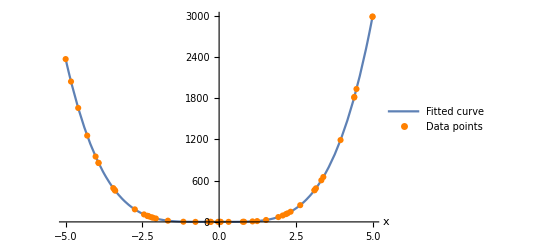
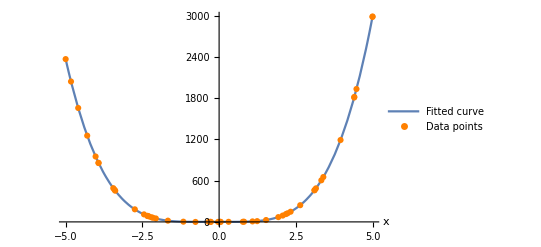
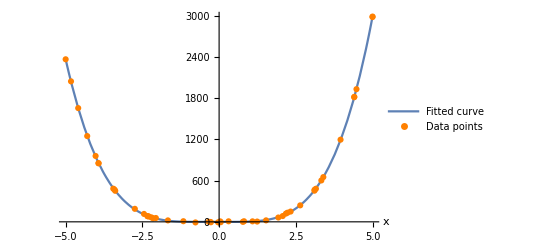
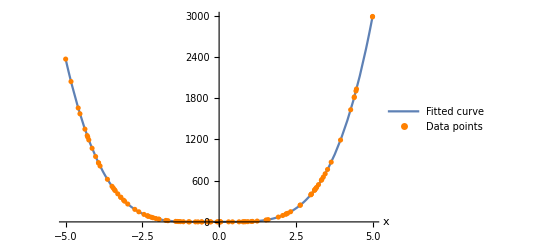
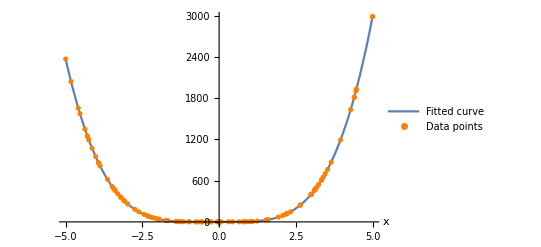
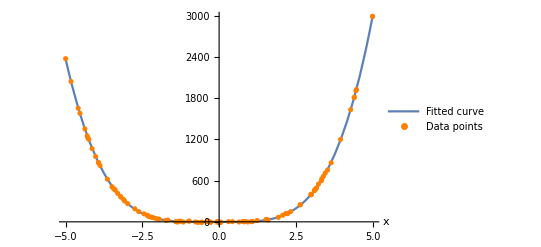
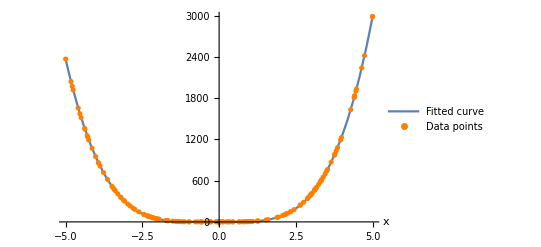
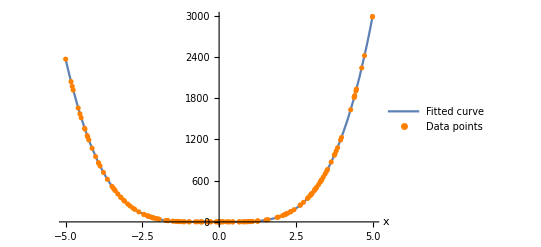

```mathematica
figs
```

### Funciones polinomiales

```mathematica
Table[Export["/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/poly_"<>IntegerString[i,10,2]<>".pdf",figs[[i]]],{i,9}]
```

{/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/poly_01.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/poly_02.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/poly_03.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/poly_04.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/poly_05.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/poly_06.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/poly_07.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/poly_08.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/poly_09.pdf}

### Funciones de Legendre

```mathematica
Table[Export["/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/legendre_"<>IntegerString[i,10,2]<>".pdf",figs[[i]]],{i,9}]
```

{/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/legendre_01.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/legendre_02.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/legendre_03.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/legendre_04.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/legendre_05.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/legendre_06.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/legendre_07.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/legendre_08.pdf,/home/jadeleon/Documents/2022-2/mscsc_2022-2/reportes_tareas/img_tarea03/legendre_09.pdf}

## Funciones polinomiales

### 50 puntos

```mathematica
f[x_,R_]:=0.4 x^4-0.5 x^3-x^2+1+R
points=Points[50,#,23409]&/@{0.1,1,10};
```

#### Matriz de covarianza

```mathematica
A=Table[(#[[1]])^i,{i,0,4}]&/@points[[1]];
MatrixForm[Round[CovarianceMatrix[A],0.001]]
```

(0.072 | 0. | -0.013 | 0. | 0.
0. | 0.014 | 0. | -0.001 | 0.
-0.013 | 0. | 0.004 | 0. | 0.
0. | -0.001 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.)

#### R∈[-0.1,0.1]

0.986273-0.00157755 x-0.999636 x^2-0.499809 x^3+0.400026 x^4

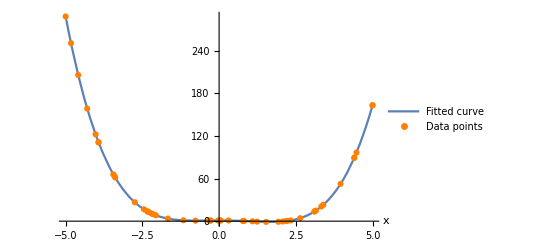

```mathematica
Plus@@Table[#[[i+1]] x^i,{i,0,4}]&[MyLeastSquares[points[[1]]]]
fig=Graphing[points[[1]],MyLeastSquares[points[[1]]]]
AppendTo[figs,fig];
```

#### R ∈ [-1, 1]

0.862413-0.0145073 x-0.996247 x^2-0.498169 x^3+0.400259 x^4

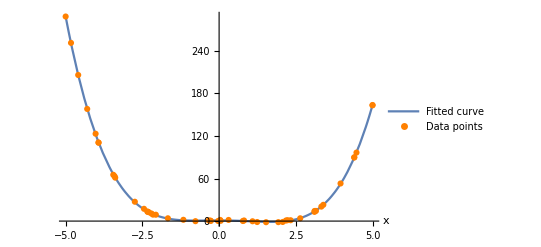

```mathematica
Plus@@Table[#[[i+1]] x^i,{i,0,4}]&[MyLeastSquares[points[[2]]]]
fig=Graphing[points[[2]],MyLeastSquares[points[[2]]]]
AppendTo[figs,fig];
```

#### R∈[-10,10]

-0.376192-0.143804 x-0.962351 x^2-0.481768 x^3+0.402582 x^4

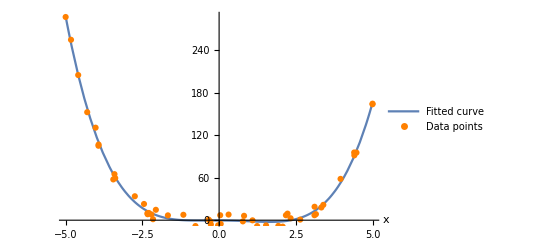

```mathematica
Plus@@Table[#[[i+1]] x^i,{i,0,4}]&[MyLeastSquares[points[[3]]]]
fig=Graphing[points[[3]],MyLeastSquares[points[[3]]]]
AppendTo[figs,fig];
```

### 100 puntos

```mathematica
f[x_,R_]:=0.4 x^4-0.5 x^3-x^2+1+R
points=Points[100,#,23409]&/@{0.1,1,10};
```

#### R∈[-0.1,0.1]

0.986895-0.00689854 x-0.996389 x^2-0.499705 x^3+0.399873 x^4

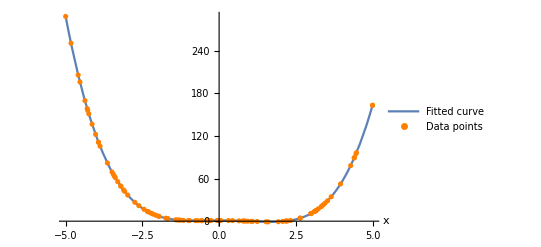

```mathematica
Plus@@Table[#[[i+1]] x^i,{i,0,4}]&[MyLeastSquares[points[[1]]]]
fig=Graphing[points[[1]],MyLeastSquares[points[[1]]]]
AppendTo[figs,fig];
```

#### R∈[-1,1]

0.866069-0.0685425 x-0.962956 x^2-0.497081 x^3+0.398685 x^4

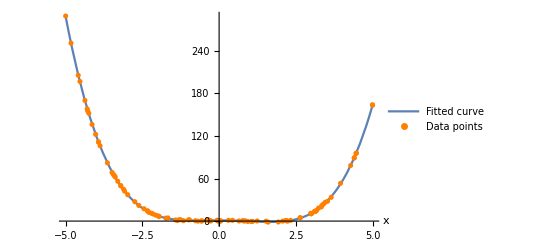

```mathematica
Plus@@Table[#[[i+1]] x^i,{i,0,4}]&[MyLeastSquares[points[[2]]]]
fig=Graphing[points[[2]],MyLeastSquares[points[[2]]]]
AppendTo[figs,fig];
```

#### R∈[-10,10]

-0.342195-0.684982 x-0.628628 x^2-0.470836 x^3+0.386812 x^4

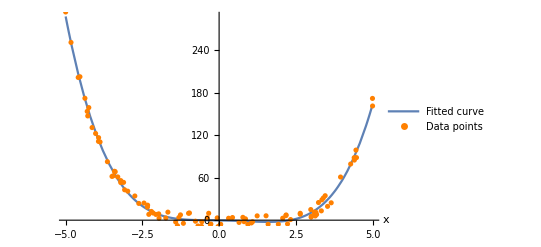

```mathematica
Plus@@Table[#[[i+1]] x^i,{i,0,4}]&[MyLeastSquares[points[[3]]]]
fig=Graphing[points[[3]],MyLeastSquares[points[[3]]]]
AppendTo[figs,fig];
```

### 150 puntos

```mathematica
f[x_,R_]:=0.4 x^4-0.5 x^3-x^2+1+R
points=Points[150,#,23409]&/@{0.1,1,10};
```

#### R∈[-0.1,0.1]

0.993142-0.00596376 x-0.998524 x^2-0.499513 x^3+0.399911 x^4

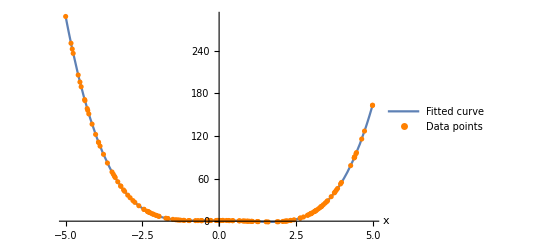

```mathematica
Plus@@Table[#[[i+1]] x^i,{i,0,4}]&[MyLeastSquares[points[[1]]]]
fig=Graphing[points[[1]],MyLeastSquares[points[[1]]]]
AppendTo[figs,fig];
```

#### R∈[-1,1]

0.939325-0.0589197 x-0.987856 x^2-0.495165 x^3+0.399229 x^4

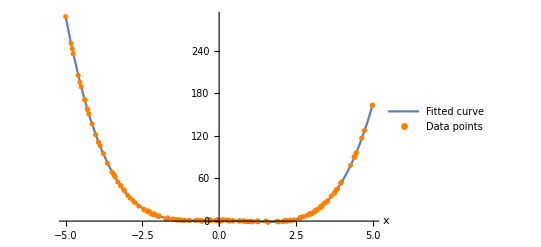

```mathematica
Plus@@Table[#[[i+1]] x^i,{i,0,4}]&[MyLeastSquares[points[[2]]]]
fig=Graphing[points[[2]],MyLeastSquares[points[[2]]]]
AppendTo[figs,fig];
```

#### R∈[-10,10]

0.401153-0.588479 x-0.881183 x^2-0.451691 x^3+0.3924 x^4

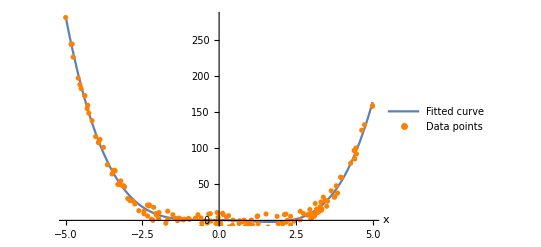

```mathematica
Plus@@Table[#[[i+1]] x^i,{i,0,4}]&[MyLeastSquares[points[[3]]]]
fig=Graphing[points[[3]],MyLeastSquares[points[[3]]]]
AppendTo[figs,fig];
```

## Polinomios de Legendre

```mathematica
f[x_]:=Plus@@(LegendreP[#,x]&/@Range[0,4]);f[x]
```

1+x+1/2 (-1+3 x^2)+1/2 (-3 x+5 x^3)+1/8 (3-30 x^2+35 x^4)

#### Matriz de covarianza

```mathematica
points=Points[50,#,23409]&/@{0.1,1,10};
A=Table[LegendreP[i,#[[1]]],{i,0,4}]&/@points[[1]];
MatrixForm[Round[CovarianceMatrix[A],0.001]]
```

(0.064 | 0. | -0.007 | 0. | 0.
0. | 0.013 | 0. | 0. | 0.
-0.007 | 0. | 0.002 | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.)

### 50 puntos

```mathematica
f[x_,R_]:=R+Plus@@(LegendreP[#,x]&/@Range[0,4]);
points=Points[50,#,23409]&/@{0.1,1,10};
```

#### R∈[-0.1,0.1]

```mathematica
Plus@@Table[#[[i+1]]LegendreP[i,x],{i,0,4}]&[MyLeastSquares[points[[1]],2]]
fig=Graphing[points[[1]],MyLeastSquares[points[[1]],2],2]
AppendTo[figs,fig];
```

0.98261+1.00066 x+0.500542 (-1+3 x^2)+0.500015 (-3 x+5 x^3)+0.124999 (3-30 x^2+35 x^4)

-Graphics-

#### R∈[-1,1]

```mathematica
Plus@@Table[#[[i+1]]LegendreP[i,x],{i,0,4}]&[MyLeastSquares[points[[2]],2]]
fig=Graphing[points[[2]],MyLeastSquares[points[[2]],2],2]
AppendTo[figs,fig];
```

0.859917+0.988717 x+0.501739 (-1+3 x^2)+0.500343 (-3 x+5 x^3)+0.125006 (3-30 x^2+35 x^4)

-Graphics-

#### R∈[-10,10]

```mathematica
Plus@@Table[#[[i+1]]LegendreP[i,x],{i,0,4}]&[MyLeastSquares[points[[3]],2]]
fig=Graphing[points[[3]],MyLeastSquares[points[[3]],2],2]
AppendTo[figs,fig];
```

-0.367014+0.869283 x+0.513712 (-1+3 x^2)+0.503623 (-3 x+5 x^3)+0.125072 (3-30 x^2+35 x^4)

-Graphics-

### 100 puntos

```mathematica
f[x_,R_]:=R+Plus@@(LegendreP[#,x]&/@Range[0,4]);
points=Points[100,#,23409]&/@{0.1,1,10};
```

#### R∈[-0.1,0.1]

```mathematica
Plus@@Table[#[[i+1]]LegendreP[i,x],{i,0,4}]&[MyLeastSquares[points[[1]],2]]
fig=Graphing[points[[1]],MyLeastSquares[points[[1]],2],2]
AppendTo[figs,fig];
```

0.987105+0.991816 x+0.501268 (-1+3 x^2)+0.500077 (-3 x+5 x^3)+0.124996 (3-30 x^2+35 x^4)

-Graphics-

#### R∈[-1,1]

```mathematica
Plus@@Table[#[[i+1]]LegendreP[i,x],{i,0,4}]&[MyLeastSquares[points[[2]],2]]
fig=Graphing[points[[2]],MyLeastSquares[points[[2]],2],2]
AppendTo[figs,fig];
```

0.877185+0.931741 x+0.512073 (-1+3 x^2)+0.500602 (-3 x+5 x^3)+0.124962 (3-30 x^2+35 x^4)

-Graphics-

#### R∈[-10,10]

```mathematica
Plus@@Table[#[[i+1]]LegendreP[i,x],{i,0,4}]&[MyLeastSquares[points[[3]],2]]
fig=Graphing[points[[3]],MyLeastSquares[points[[3]],2],2]
AppendTo[figs,fig];
```

-0.222015+0.330991 x+0.620124 (-1+3 x^2)+0.505851 (-3 x+5 x^3)+0.124623 (3-30 x^2+35 x^4)

-Graphics-

### 150 puntos

```mathematica
f[x_,R_]:=R+Plus@@(LegendreP[#,x]&/@Range[0,4]);
points=Points[150,#,23409]&/@{0.1,1,10};
```

#### R∈[-0.1,0.1]

```mathematica
Plus@@Table[#[[i+1]]LegendreP[i,x],{i,0,4}]&[MyLeastSquares[points[[1]],2]]
fig=Graphing[points[[1]],MyLeastSquares[points[[1]],2],2]
AppendTo[figs,fig];
```

0.995401+0.992907 x+0.500262 (-1+3 x^2)+0.500115 (-3 x+5 x^3)+0.124998 (3-30 x^2+35 x^4)

-Graphics-

#### R∈[-1,1]

```mathematica
Plus@@Table[#[[i+1]]LegendreP[i,x],{i,0,4}]&[MyLeastSquares[points[[2]],2]]
fig=Graphing[points[[2]],MyLeastSquares[points[[2]],2],2]
AppendTo[figs,fig];
```

0.945002+0.942552 x+0.503623 (-1+3 x^2)+0.500984 (-3 x+5 x^3)+0.124979 (3-30 x^2+35 x^4)

-Graphics-

#### R∈[-10,10]

```mathematica
Plus@@Table[#[[i+1]]LegendreP[i,x],{i,0,4}]&[MyLeastSquares[points[[3]],2]]
fig=Graphing[points[[3]],MyLeastSquares[points[[3]],2],2]
AppendTo[figs,fig];
```

0.44101+0.439003 x+0.537231 (-1+3 x^2)+0.50968 (-3 x+5 x^3)+0.124784 (3-30 x^2+35 x^4)

-Graphics-